## Basic usage and computing A,B.

Here is a notebook that explains how to interact with the data (JSON files) generated by the ocaml program.

The directory structure of the repository where this file is located looks like

adam@adam-ThinkPad-T580:~/src/gits/BIL-numerical-T2$ tree -d -L 1 -I “_build|_opam” ./
./
├── initial_data
├── long_runs
├── test
└── utilities

4 directories

This file is in the utilities directory, and you should open it by double clicking there. When you open it, by default, paths are relative to your home directory. The following command sets paths to be relative to the directory where this file (t2_data.nb) is located. Click anywhere in the following cell and evaluate the cell to make the change. (On my machine, I type shift+enter to evaluate a cell.)

```mathematica
SetDirectory[NotebookDirectory[]]
```

/home/adam/src/gits/BIL-numerical-T2/utilities

If you evaluated it correctly, the output should be the full path to the directory where t2_data.nb is located.

The json data are located in “../long_runs”. We can list the contents of that directory with the following command. The output of this command is long, so we only return the first four elements by feeding the output of the FileNames function into the Take function.

```mathematica
FileNames["*","../long_runs"]//Take[#,4]&
```

{../long_runs/stop,../long_runs/t_b0_0_1024.1.json,../long_runs/t_b0_0_1024.json,../long_runs/t_b0_0_2048.1.json}

Here is a simpler example to make the role of the // operator more clear:

```mathematica
{1,2,3,4,5,6,7,8,9,10}//Take[#,7]&
```

{1,2,3,4,5,6,7}

This is exactly the same as evaluating

```mathematica
Take[{1,2,3,4,5,6,7,8,9,10},7]
```

{1,2,3,4,5,6,7}

Let’s see what we get when we import one of these json files:

```mathematica
Import["../long_runs/t_b0_0_512.1.json"]
```

{initial time→0.,5,evolution→{{time→0.,data→{1}},507,{time→20.999,data→{{-17.472,-17.472,509,-17.472},4,{1}}}}}
 |  |  |  |

This takes quite some time, and returns a list that has the form { name1 -> value1 , name2 -> value2 , ... }. It’s better to assign this to a name so we can manipulate it more easily.

```mathematica
exampleimport =Import["../long_runs/t_b0_0_512.1.json"];
```

The semicolon at the end of the above line suppresses anything from being printed in the output cell.

Let’s look at this thing called exampleimport.

```mathematica
exampleimport//Head
```

List

exampleimport has type List

```mathematica
exampleimport//Length
```

7

the list is 7 elements long

```mathematica
exampleimport[[1]]
```

initial time→0.

this is the first element

```mathematica
exampleimport//Map[First]
```

{initial time,fourier coefficients,time limit,checkpoint size,resolution,print frequency,evolution}

Map[...] applies some function to every element of a list. In this case the function that we apply is First. This is just just returns the first element of an object. Since each element in exampleimport has the form nameN -> valueN, First[nameN -> valueN] just returns nameN.

For plotting, we only need the part “evolution”. We could pick this out using

```mathematica
exampleimport[[7,2]]
```

{{time→0.,data→{{0.951703,0.963582,0.975029,0.986036,504,0.900038,0.913559,0.926683,0.939401},4,{1}}},507,{1,1}}
 |  |  |  |

That is, take the 7th part of exampleimport, then take the 2nd part of that.

An easier way to do it is

```mathematica
exampleevolution="evolution"/.exampleimport
```

{{time→0.,data→{{0.951703,0.963582,0.975029,0.986036,504,0.900038,0.913559,0.926683,0.939401},4,{1}}},507,{1,1}}
 |  |  |  |

If we cared to, we could also get other information from exampleimport

```mathematica
"resolution"/.exampleimport
```

512

The thing we have assigned to the name exampleevolution is also a list:

```mathematica
exampleevolution//Head
```

List

Each of its elements has the following form:

```mathematica
exampleevolution//First//ToString//StringTake[#,1000]&
```

{time -> 0., data -> {{0.951703, 0.963582, 0.975029, 0.986036, 0.996596, 1.0067, 1.01634, 1.02552, 1.03422, 1.04244, 1.05017, 1.05741, 1.06416, 1.0704, 1.07615, 1.08138, 1.0861, 1.09031, 1.094, 1.09717, 1.09982, 1.10194, 1.10355, 1.10463, 1.10518, 1.10521, 1.10472, 1.1037, 1.10216, 1.1001, 1.09753, 1.09444, 1.09083, 1.08672, 1.08209, 1.07697, 1.07135, 1.06523, 1.05863, 1.05154, 1.04398, 1.03594, 1.02744, 1.01848, 1.00907, 0.999219, 0.98893, 0.978212, 0.967076, 0.955528, 0.94358, 0.931238, 0.918515, 0.905418, 0.89196, 0.878149, 0.863997, 0.849515, 0.834715, 0.819607, 0.804203, 0.788516, 0.772559, 0.756342, 0.73988, 0.723184, 0.706269, 0.689147, 0.671832, 0.654337, 0.636677, 0.618865, 0.600916, 0.582843, 0.564661, 0.546385, 0.528029, 0.509607, 0.491136, 0.472628, 0.454101, 0.435567, 0.417044, 0.398544, 0.380085, 0.361681, 0.343346, 0.325097, 0.306948, 0.288915, 0.271013, 0.253256, 0.235661, 0.218241, 0.201012, 0.183988, 0.167185, 0.150617, 0.134298, 0.118244, 0.102468, 0.0869849, 0.07180

We used //ToString//StringTake[#,1000]& to truncate the long output.

Let’s finally look at the information contained in the “data” field.

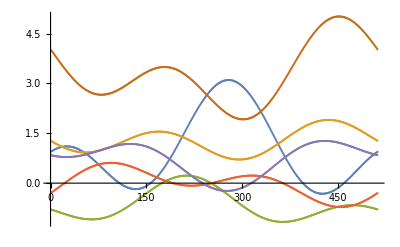

```mathematica
exampleevolution//First//"data"/.#&//ListPlot
```

exampleevolution is a list of what we might call “timeframes”; objects of the form { “time” -> ... , “data” -> { ... } }

exampleevolution//First is the first timeframe that we printed above: {time -> 0., data -> {{0.951703, 0.96 .... }} }

exampleevolution//First//”data”/.#& is the data part of the first timeframe. It is a list of length 6. Each element is a list of floats that encodes the function values in the order { p , pi_p , q , pi_q , lambda , pi_lambda }. The plot above is then these 6 functions.

One might wonder why I should include a field labeled “time”. Recall that Δt is not the same throughout the run.

This is rather convoluted, so we can shorthand this process. We define the function

```mathematica
p[timeframe_]:=("data"/.timeframe)[[1]]
```

which takes a timeframe, gets its data component, and takes the first element of the data component, which we know is the function p.

Then we can write simply

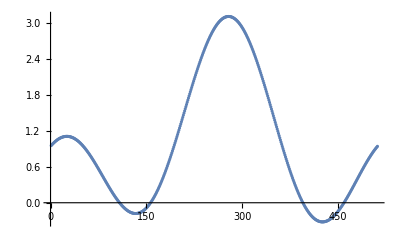

```mathematica
exampleevolution//First//p//ListPlot
```

Since exampleevolution is a list of timeframes, we can define a function which takes a timeframe as an input

```mathematica
τ[timeframe_]:=("time"/.timeframe)
point[timeframe_]:={τ[timeframe],Mean[p[timeframe]]} (* x is the time of the timeframe, y is the mean of P over that timeframe. *)
```

and map that function over the list exampleevolution.

```mathematica
exampleevolution//Map[point]//ToString//StringTake[#,1000]&
```

{{0., 0.982405}, {0.051056, 0.96661}, {0.114923, 0.938368}, {0.180396, 0.905273}, {0.244703, 0.870449}, {0.307382, 0.834967}, {0.36816, 0.799452}, {0.426895, 0.764299}, {0.483532, 0.729761}, {0.538075, 0.696}, {0.590568, 0.663114}, {0.641079, 0.631156}, {0.689687, 0.600152}, {0.736481, 0.570104}, {0.781553, 0.541}, {0.824993, 0.512821}, {0.866891, 0.48554}, {0.90733, 0.459127}, {0.965431, 0.421064}, {1.02069, 0.38477}, {1.07334, 0.350135}, {1.12358, 0.317052}, {1.17162, 0.285422}, {1.21761, 0.255151}, {1.26171, 0.226152}, {1.30407, 0.198346}, {1.34481, 0.171658}, {1.39679, 0.1377}, {1.44632, 0.105464}, {1.49362, 0.074823}, {1.53887, 0.0456586}, {1.58222, 0.0178668}, {1.62384, -0.00864637}, {1.66385, -0.0339655}, {1.71177, -0.0640507}, {1.75756, -0.0925223}, {1.8014, -0.119498}, {1.84343, -0.145084}, {1.88381, -0.169374}, {1.93024, -0.196927}, {1.97465, -0.222864}, {2.01721, -0.247299}, {2.05805, -0.270333}, {2.10372, -0.29556}, {2.14742, -0.319136}, {2.18931, -0.341177}, {2.22954, -0.3

Again, the output is long so we truncate it. We can plot these (x,y) pairs.

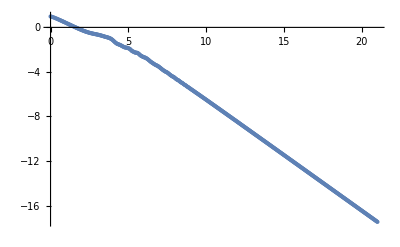

```mathematica
exampleevolution//Map[point]//ListPlot
```

Okay, now we know how to take a file and get a list of timeframes from it. And we know how to define a function that acts on timeframes and evaluate it on the timeframes stored in that file. Evaluate the next cell to define a bunch of functions which act on timeframes. We already defined the functions p and τ above, but we can redefine them here without hurting anything.

```mathematica
(* Functions one can calculate on each time frame. *)
p[timeframe_]:=("data"/.timeframe)[[1]]
πp[timeframe_]:=("data"/.timeframe)[[2]]
q[timeframe_]:=("data"/.timeframe)[[3]]
πq[timeframe_]:=("data"/.timeframe)[[4]]
λ[timeframe_]:=("data"/.timeframe)[[5]]
πλ[timeframe_]:=("data"/.timeframe)[[6]]
τ[timeframe_]:=("time"/.timeframe)
α[timeframe_]:=1/(2πλ[timeframe])^2
v[timeframe_]:=p[timeframe]+τ[timeframe]
ρ[timeframe_]:=-1/2 Log[α[timeframe]]
l[timeframe_]:=p[timeframe]+1/2λ[timeframe]-3/2τ[timeframe]-Log[2]
Ptau[timeframe_]:=-πp[timeframe]/(2*πλ[timeframe])
Qtau[timeframe_]:=-Exp[-2p[timeframe]]πq[timeframe]/(2*πλ[timeframe])
Vtau[timeframe_]:=Ptau[timeframe]+1
ρtau[timeframe_]:=Exp[l[timeframe]]
ltau[tf_]:=-2-ρtau[tf]+1/2En[tf]
A[timeframe_]:=Mean[-πp[timeframe]+2πλ[timeframe]+q[timeframe]*πq[timeframe]];
B[timeframe_]:=Mean[-πq[timeframe]];
c[tf_]:=Mean[(Qtau[tf]-2q[tf]+q[tf]Vtau[tf])2 πλ[tf]+q[tf](-πp[tf]+2πλ[tf]+q[tf]*πq[tf])];
```

Note that we defined how to calculate A and B from a timeframe here.

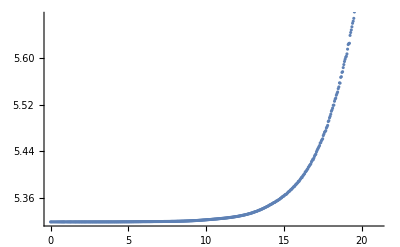

```mathematica
point[timeframe_]:={τ[timeframe],A[timeframe]}
exampleevolution//Map[point]//ListPlot
```

This doesn't look very constant, but remember that we’re looking at a low resolution run, and if you look at the scale on the left it makes the situation seem less bad.

Okay, now what is the process of going from a file to the value of A? Let’s go back and look at the output of FileNames[“*”,”../long_runs”] again.

```mathematica
FileNames["*","../long_runs"]//Take[#,20]&//TableForm
```

../long_runs/stop
../long_runs/t_b0_0_1024.1.json
../long_runs/t_b0_0_1024.json
../long_runs/t_b0_0_2048.1.json
../long_runs/t_b0_0_2048.json
../long_runs/t_b0_0_4096.1.json
../long_runs/t_b0_0_4096.json
../long_runs/t_b0_0_512.1.json
../long_runs/t_b0_0_512.json
../long_runs/t_b0_121_1024.1.json
../long_runs/t_b0_121_1024.json
../long_runs/t_b0_121_2048.1.json
../long_runs/t_b0_121_2048.json
../long_runs/t_b0_121_4096.1.json
../long_runs/t_b0_121_4096.json
../long_runs/t_b0_121_512.1.json
../long_runs/t_b0_121_512.json
../long_runs/t_b0_13_1024.1.json
../long_runs/t_b0_13_1024.json
../long_runs/t_b0_13_2048.1.json

What are all these files? t_ is just a prefix for the data output by the simulation program. The next part is either b0_, pol_, or gen_ depending on whether the initial data is B_0, polarised, or generic. The next number is between 0 and 199 inclusive and is just the label of the run. The next field is either 512, 1024, 2048, or 4096 and indicates the spatial resolution. But why are there two “t_b0 _ 0_ 1024” files? That is, t_b0_0_1024.json and t_b0_0_1024.1.json. If we import the first one, we can see what is going on:

```mathematica
"evolution"/.Import["../long_runs/t_b0_0_1024.json"]//Length
```

1

So the file t_b0_0_1024.json only has one timeframe in its “evolution” field. This is the data at the initial time, which has been generated from the Fourier coefficients. When the OCaml program runs, it reads this file and uses the initial data to start the simulation. When it outputs data, however, it writes files t_b0_0_1024.1.json, t_b0_0_1024.2.json et cetera until it reaches the specified final time.

Okay, if we want to calculate A for every piece of initial data, then we only need the initial data file, not the full evolution files *.1.json , *.2.json and so on. So let’s get a list of just these initial data files.

```mathematica
FileNames["*","../long_runs"]//Select[Not[StringMatchQ[#,"*.1.json"]||StringMatchQ[#,"*.2.json"]]&]//Take[#,20]&//TableForm
```

../long_runs/stop
../long_runs/t_b0_0_1024.json
../long_runs/t_b0_0_2048.json
../long_runs/t_b0_0_4096.json
../long_runs/t_b0_0_512.json
../long_runs/t_b0_121_1024.json
../long_runs/t_b0_121_2048.json
../long_runs/t_b0_121_4096.json
../long_runs/t_b0_121_512.json
../long_runs/t_b0_13_1024.json
../long_runs/t_b0_13_2048.json
../long_runs/t_b0_13_4096.json
../long_runs/t_b0_13_512.json
../long_runs/t_b0_139_1024.json
../long_runs/t_b0_139_2048.json
../long_runs/t_b0_139_4096.json
../long_runs/t_b0_139_512.json
../long_runs/t_b0_162_1024.json
../long_runs/t_b0_162_2048.json
../long_runs/t_b0_162_4096.json

Note that we still get 4 initial data files for each piece of initial data: one for each of the four resolutions. To calculate A, though, we only need one of these. So let’s just select the 512 resolution ones.

```mathematica
FileNames["*_512.json","../long_runs"]//Take[#,20]&//TableForm
```

../long_runs/t_b0_0_512.json
../long_runs/t_b0_121_512.json
../long_runs/t_b0_13_512.json
../long_runs/t_b0_139_512.json
../long_runs/t_b0_162_512.json
../long_runs/t_b0_172_512.json
../long_runs/t_b0_179_512.json
../long_runs/t_b0_180_512.json
../long_runs/t_b0_190_512.json
../long_runs/t_b0_24_512.json
../long_runs/t_b0_26_512.json
../long_runs/t_b0_43_512.json
../long_runs/t_b0_58_512.json
../long_runs/t_b0_61_512.json
../long_runs/t_b0_64_512.json
../long_runs/t_b0_81_512.json
../long_runs/t_b0_85_512.json
../long_runs/t_b0_89_512.json
../long_runs/t_b0_9_512.json
../long_runs/t_gen_0_512.json

Okay, now that we have the files we want to act on, let’s write a function that takes a file and produces the triple { filename , A , B }.

```mathematica
f[filename_]:=Module[{import,evo,firstframe}, (* wrapping this in a Module box ensures that import, evo, and firstframe have local scope. *)
import=Import[filename];
evo="evolution"/.import;
firstframe=evo//First;
{filename, A[firstframe],B[firstframe]}
]
f["../long_runs/t_b0_9_512.json"]
```

{../long_runs/t_b0_9_512.json,3.16677,-1.70762×10^-18}

Now we can map this function over all the files produced by FileNames[“*_512.json”,”../long_runs”] to get them packed into a nice list.

```mathematica
abdata=FileNames["*_512.json","../long_runs"]//Map[f]
```

{{../long_runs/t_b0_0_512.json,5.31887,-2.68882×10^-17},{../long_runs/t_b0_121_512.json,3.35561,1.24683×10^-18},{../long_runs/t_b0_13_512.json,9.08415,2.42861×10^-17},{../long_runs/t_b0_139_512.json,9.08684,2.28767×10^-17},{../long_runs/t_b0_162_512.json,4.54853,-3.51282×10^-17},{../long_runs/t_b0_172_512.json,4.72947,-2.79724×10^-17},{../long_runs/t_b0_179_512.json,1.78583,5.0822×10^-19},{../long_runs/t_b0_180_512.json,-11.5762,-7.97973×10^-17},{../long_runs/t_b0_190_512.json,1.00831,3.84892×10^-18},{../long_runs/t_b0_24_512.json,14.2229,-1.14492×10^-16},{../long_runs/t_b0_26_512.json,0.523264,-2.34188×10^-17},{../long_runs/t_b0_43_512.json,1.75625,-1.0842×10^-17},{../long_runs/t_b0_58_512.json,4.56765,1.05168×10^-17},{../long_runs/t_b0_61_512.json,10.3372,4.46691×10^-17},{../long_runs/t_b0_64_512.json,6.11423,1.6263×10^-17},{../long_runs/t_b0_81_512.json,7.82669,3.13741×10^-18},{../long_runs/t_b0_85_512.json,7.58898,2.20229×10^-18},{../long_runs/t_b0_89_512.json,1.09303,-5.11743×10^-17},{../long_runs/t_b0_9_512.json,3.16677,-1.73472×10^-18},{../long_runs/t_gen_0_512.json,4.41178,-0.978214},{../long_runs/t_gen_121_512.json,3.28582,0.239005},{../long_runs/t_gen_13_512.json,8.7913,-0.126832},{../long_runs/t_gen_139_512.json,8.51905,0.344777},{../long_runs/t_gen_156_512.json,1.68018,0.957317},{../long_runs/t_gen_162_512.json,4.30096,-0.924357},{../long_runs/t_gen_163_512.json,-2.30351,0.3552},{../long_runs/t_gen_172_512.json,5.02524,0.408361},{../long_runs/t_gen_179_512.json,1.38711,0.810813},{../long_runs/t_gen_190_512.json,4.02756,0.914832},{../long_runs/t_gen_192_512.json,2.60474,0.539019},{../long_runs/t_gen_24_512.json,5.00432,0.897163},{../long_runs/t_gen_43_512.json,2.15162,0.211017},{../long_runs/t_gen_58_512.json,3.60469,0.748498},{../long_runs/t_gen_61_512.json,11.8741,-0.724321},{../long_runs/t_gen_64_512.json,6.03403,0.0421757},{../long_runs/t_gen_69_512.json,2.60493,-0.484623},{../long_runs/t_gen_81_512.json,9.337,-0.425272},{../long_runs/t_gen_85_512.json,8.06716,-0.90557},{../long_runs/t_gen_90_512.json,1.97636,0.40878},{../long_runs/t_gen_9_512.json,2.46403,-0.705462},{../long_runs/t_pol_104_512.json,5.71051,0.},{../long_runs/t_pol_105_512.json,8.37147,0.},{../long_runs/t_pol_107_512.json,7.6022,0.},{../long_runs/t_pol_108_512.json,4.37429,0.},{../long_runs/t_pol_113_512.json,6.46319,0.},{../long_runs/t_pol_124_512.json,15.8985,0.},{../long_runs/t_pol_131_512.json,23.6665,0.},{../long_runs/t_pol_144_512.json,6.23928,0.},{../long_runs/t_pol_151_512.json,7.9945,0.},{../long_runs/t_pol_164_512.json,7.41415,0.},{../long_runs/t_pol_167_512.json,8.98571,0.},{../long_runs/t_pol_168_512.json,-15.0374,0.},{../long_runs/t_pol_186_512.json,0.000113536,0.},{../long_runs/t_pol_193_512.json,2.24356,0.},{../long_runs/t_pol_196_512.json,2.46365,0.},{../long_runs/t_pol_197_512.json,11.5672,0.},{../long_runs/t_pol_3_512.json,5.47366,0.},{../long_runs/t_pol_90_512.json,3.06358,0.}}

It’s then possible to export this as a tsv if we want. Since abdata is a list of lists, exporting to a tsv puts each element eg {../long_runs/t_pol_105_512.json,8.37147,0.} on its own line.

```mathematica
Export["abdata.tsv",abdata]
```

abdata.tsv

This file appears in the working directory, which we set at the first line of the notebook to be the notebook directory (where t2_data.nb is located).

## Advanced usage and computing arbitrary functions along a run.

Now that we can read a file and compute functions from the data in that file, let’s look at some more examples.

First, in addition to the functions acting on time frames above, we might want to compute functions involving spatial derivatives. To that end we define

```mathematica
(* Computes a finite-difference spatial derivative of a function on a time frame. *)
spacederivative[f_,tf_]:=Module[{temp,n,Δx},
temp=f[tf];
n=Length[temp];
Δx=2 Pi / n;
temp=Join[
{temp[[n-1]]},
{temp[[n]]},
temp,
{temp[[1]]},
{temp[[2]]}
];
Table[(2/3*(temp[[i+1]]-temp[[i-1]])+1/12*(temp[[i-2]]-temp[[i+2]]))/Δx,{i,1+2,n+2}]
]
```

This allows us to give the definition of λtau, the constraint, and some other things

```mathematica
λtau[tf_]:=1/(2*πλ[tf])^2(
πp[tf]^2+Exp[-2p[tf]]πq[tf]^2+Exp[-2τ[tf]]spacederivative[p,tf]^2+Exp[2(p[tf]-τ[tf])]spacederivative[q,tf]^2
)+Exp[(λ[tf]+2p[tf]+3τ[tf])/2]

(* Calculate the constraint. Note that this is pointwise in space. This should be identically 0 for solutions without error. *)
galconstraint[tf_]:=Module[{dp,dq,dλ},
 dp=spacederivative[p,tf];
 dq=spacederivative[q,tf];
 dλ=spacederivative[λ,tf];
(dp*πp[tf])+(dq*πq[tf])+(dλ*πλ[tf])
]
galconstraintavg[tf_]:=Mean[galconstraint[tf]]

(* More functions that can be computed on time frames. *)
Ev[tf_]:=Vtau[tf]^2+Exp[2(τ[tf]-ρ[tf])]spacederivative[p,tf]^2
Eq[tf_]:=Exp[2(v[tf]-τ[tf])](Qtau[tf]^2+Exp[2(τ[tf]-ρ[tf])]spacederivative[q,tf]^2)
En[tf_]:=Ev[tf]+Eq[tf]
J[tf_]:=1/2 En[tf]
mE[tf_]:=Mean[Exp[ρ[tf]-2τ[tf]] J[tf]]
Π[tf_]:=Mean[Exp[ρ[tf]] ]
Λ[tf_]:=1/2Mean[Exp[-2τ[tf]+ρ[tf]]Vtau[tf](v[tf]-Mean[v[tf]]-1)]
H[tf_]:=Π[tf](mE[tf]+Λ[tf])
Y[tf_]:=Mean[Exp[l[tf]+ρ[tf]+2τ[tf]]]
cc[tf_]:=Π[tf]Exp[-τ[tf]]H[tf]^(-1/2)
dd[tf_]:=Y[tf]Exp[-3τ[tf]]H[tf]^(-1/2)

(* The terms from Beverly's superhamiltonian. The 'a' versions below just have an extra factor of 1/πλ so that they are O(1) generically. *)
H0[timeframe_]:=πp[timeframe]*πp[timeframe]/(4*πλ[timeframe])
Hkin[tf_]:=Exp[-2 p[tf]] πq[tf]*πq[tf]/(4*πλ[tf])
Hsmall[tf_]:=Exp[2 τ[tf]] spacederivative[p,tf]*spacederivative[p,tf]/(4*πλ[tf])
Hcurv[tf_]:=Exp[2 τ[tf]]Exp[2 p[tf]]spacederivative[q,tf]*spacederivative[q,tf]/(4*πλ[tf])
Htwist[tf_]:=πλ[tf] Exp[-3τ[tf]/2]Exp[λ[tf]/2+p[tf]]

H0a[timeframe_]:=πp[timeframe]*πp[timeframe]/(4*πλ[timeframe]*πλ[timeframe])
Hkina[tf_]:=Exp[-2 p[tf]] πq[tf]*πq[tf]/(4*πλ[tf]*πλ[tf])
Hsmalla[tf_]:=Exp[2 τ[tf]] spacederivative[p,tf]*spacederivative[p,tf]/(4*πλ[tf]*πλ[tf])
Hcurva[tf_]:=Exp[2 τ[tf]]Exp[2 p[tf]]spacederivative[q,tf]*spacederivative[q,tf]/(4*πλ[tf]*πλ[tf])
Htwista[tf_]:= Exp[-3τ[tf]/2]Exp[λ[tf]/2+p[tf]]
```

Unfortunately, at this point it is wise to define our own import function for JSON files. I discovered I needed at this at some point when I ran into the bug described here https://mathematica.stackexchange.com/questions/163825/problem-to-import-numbers-longer-than-19-digit-with-json-or-rawjson .

It isn’t necessary to understand this function. It operates just like Import but circumvents the error.

```mathematica
myimport[path_]:=Module[{text,timeframes},
Import[path,"Text"]//StringReplace[{"{"->"<|","}"->"|>",":"->"->","["->"{","]"->"}","e+"~~s_:>" 10^"~~s,"e-"~~s_:>" 10^-"~~s}]//ToExpression
]
```

At the end of the last section, we imported a bunch of files and applied a function to all of them. Let’s look at another example.

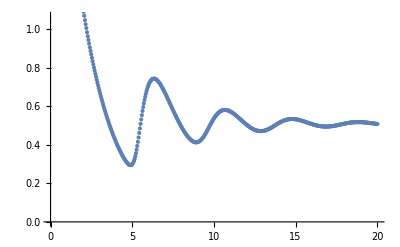

```mathematica
point[tf_]:={ τ[tf] , Exp[-τ[tf]/2]Mean[πλ[tf]] } 

Module[{evo,timeframes},
evo=myimport["../long_runs/t_b0_121_1024.1.json"];
timeframes="evolution"/.evo;
timeframes//Map[point]//ListPlot
]
```

We wrap the actual import and the computation of the data points in a Module so that Mathematica knows not to keep those in the memory once it is done outputting the plot. (Remember, Module tells Mathematica to make evo and timeframes local in scope.)

We might want to plot a lot of things repeatedly, with small changes, to it seems like a good idea to wrap the code above in a function. The function takes as input a filename and a function and returns a list of (x,y) pairs.

```mathematica
(* Returns a nice (x,y) table after applying the function f to all the time frames. *)
ClearAll[pairs];
pairs[file_,f_]:=Module[{evo,timeframes},
evo=file//myimport;
timeframes="evolution"/.evo;
Table[
{ τ[i] ,f[i] }
,{i,timeframes}]//Sort[#,#1[[1]]<#2[[1]]&]&
]
```

The last Sort command just sorts the (x,y) pairs by the value in the x place. Note that this function just returns a list of ordered pairs. We have to send the output to ListPlot to get a picture.

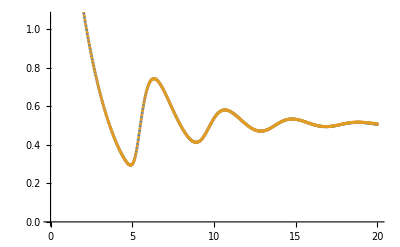

```mathematica
{
pairs["../long_runs/t_b0_121_512.1.json",Exp[-τ[#]/2]Mean[πλ[#]] &  ]
,pairs["../long_runs/t_b0_121_1024.1.json",Exp[-τ[#]/2]Mean[πλ[#]] &  ]
}//ListPlot
```

That works quite nicely, but it takes a long time to compute. Why? Because each time we run the pairs function, we read the entire JSON file from the disk which is slow. If you’re just working with one file for a while and creating many different plots, it makes sense to just import that file into the Mathematica session and plot what you need from there. But what if we want to plot across a lot of different files? It would make sense to save what we have already computed, and only reload the file if 1) the file has changed or 2) we’re computing something we haven’t previously computed. We can do this through memoization. Look at the following helper function:

```mathematica
ClearAll[pairshelper];
pairshelper[file_,f_,size_,date_]:=pairshelper[file,f,size,date]=Module[{evo,timeframes},
evo=file//myimport;
timeframes="evolution"/.evo;
Table[
{ τ[i] ,f[i] }
,{i,timeframes}]//Sort[#,#1[[1]]<#2[[1]]&]&
]


ClearAll[pairs];
pairs[file_,f_]:=pairshelper[file,f,file//FileByteCount,file//FileDate//UnixTime];
```

Now when we call the pairs function, it calculates the size and last modification time of the file we’re looking at at passes those four parameters to pairshelper. pairshelper computes the result in exactly the same way that our old pairs function did, but there is an extra bit before the Module invocation. This tells Mathematica to save the result of the computation, and if pairshelper is called with exactly the same arguments a second time, return the saved result and don’t read the file again.

Let’s try the computation we did above again:

```mathematica
AbsoluteTiming[{
pairs["../long_runs/t_b0_121_512.1.json",Exp[-τ[#]/2]Mean[πλ[#]] &  ]
,pairs["../long_runs/t_b0_121_1024.1.json",Exp[-τ[#]/2]Mean[πλ[#]] &  ]
}//ListPlot]
```

{9.99525,-Graphics-}

The first time we run it, it takes a few seconds because it has to read the two large JSON files. If we evaluate the same expression again, however

```mathematica
AbsoluteTiming[{
pairs["../long_runs/t_b0_121_512.1.json",Exp[-τ[#]/2]Mean[πλ[#]] &  ]
,pairs["../long_runs/t_b0_121_1024.1.json",Exp[-τ[#]/2]Mean[πλ[#]] &  ]
}//ListPlot]
```

{0.04153,-Graphics-}

It returns a result almost immediately. This is because the file has not changed and the function we’re evaluating on it has not changed either.

Before we move on, there are two modifications to the helper function we should make. It’s not necessary to understand these.

1) If the underlying file has changed, we should delete old memoized values.
2) If the data is split across multiple JSON files, we should read data from all the files.

```mathematica
ClearAll[pairshelper2];
pairshelper2[file_,f_,size_,date_]:=pairshelper2[file,f,size,date]=Module[{data,timeframes},
PrintTemporary[file];
pairshelper2//DownValues//Map[#[[1]]&]//Select[StringMatchQ[ToString[#],___~~file~~___]&]//Select[StringMatchQ[ToString[#],___~~ToString[f]~~___]&]//Map[(#=.)&]; (* Clear previous memoizations for this function and file if they exist. *)
data=file//myimport;
timeframes=("evolution"/.data);
Table[{τ[i],f[i]},{i,timeframes}]
]

ClearAll[pairshelper1];
pairshelper1[file_,f_]:=pairshelper2[file,f,file//FileByteCount,file//FileDate//UnixTime]

files[file_]:=Module[{root,dir,reses,filenames},
dir=DirectoryName[file];
root=FileBaseName[file];
FileNames[root<>".*.json",{dir}]
]

ClearAll[pairs];
pairs[file_,f_]:=Module[{fls,out},
fls=files[file]//Flatten;
out=Table[
j->pairshelper1[j,f]
,{j,fls}]//Flatten[#,1]&;
(files[file]/.out)//Flatten[#,1]&//SortBy[#[[1]]&]
]
```

The run t_gen_24_2048 has output data split across two files. Now pairs loads data from both before sorting the output.

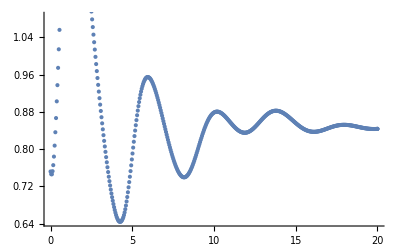

```mathematica
pairs["../long_runs/t_gen_24_2048.json",Exp[-τ[#]/2]Mean[πλ[#]] &  ]//ListPlot
```

## Below here is code from the earlier version of this notebook. Note that some of the code might be broken because I changed the names of some functions above here. Hopefully there is still something to be learned from it. I’ll try to clean it up more later.

58

{b0_0,gen_0,b0_9,b0_13,b0_24,b0_26,b0_43,b0_58,b0_61,b0_64,b0_81,b0_85,b0_89,b0_121,b0_139,b0_162,b0_172,b0_179,b0_180,b0_190,gen_9,gen_13,gen_24,gen_43,gen_58,gen_61,gen_64,gen_69,gen_81,gen_85,gen_90,gen_121,gen_139,gen_156,gen_162,gen_163,gen_172,gen_179,gen_190,gen_192,pol_3,pol_90,pol_104,pol_105,pol_107,pol_108,pol_113,pol_124,pol_131,pol_144,pol_151,pol_164,pol_167,pol_168,pol_186,pol_193,pol_196,pol_197}

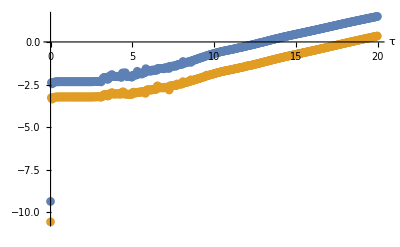
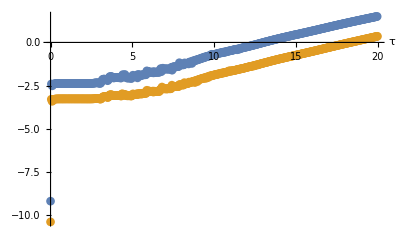
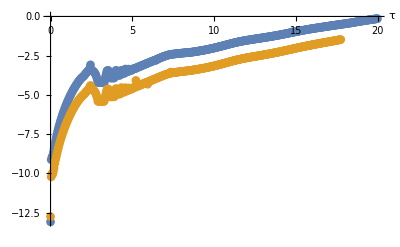
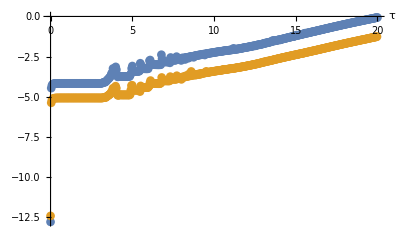
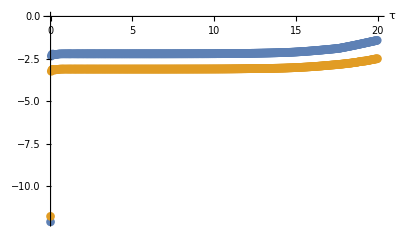
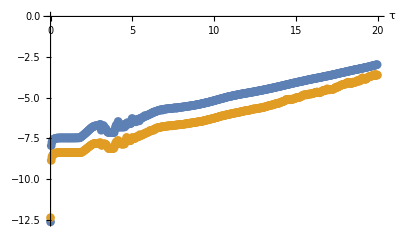
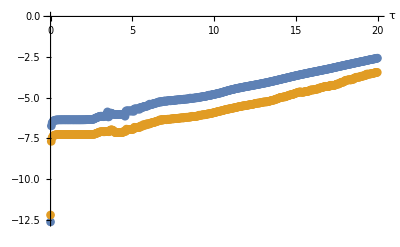
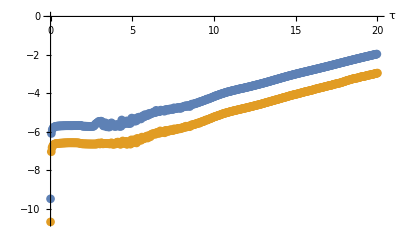
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- |  |

```mathematica
Module[{type,filenames,runs,filess,k,print,i},
filenames=FileNames["*t_*.1.json",{dir}];
i=0;
runs=filenames//StringReplace[dir<>"t_"~~typeandnum__~~"_"~~__~~".json"->typeandnum]//Union//SortBy[ToExpression[#]&]//#[[;;]]&;
Print[runs//Length];
Print[runs];
Module[{tmp},
tmp=
Monitor[
Table[  (* For each run... *)
{
filee
,apnp[  (* ... get all the data from all the files ... *)
dir<>"t_"<>filee<>".json"
,{
galconstraint/*Abs/*Max/*Log10
,1/Π[#]Mean[Exp[ρ[#]]Ev[#]]&
,1/Π[#]Mean[Exp[ρ[#]]Eq[#]]&
,Mean[(l[#]-Log[1/2])]Exp[τ[#]/4]&
,Mean[(ρ[#]-τ[#]/2)Exp[ρ[#]]]/Mean[Exp[ρ[#]]]&
}[[1]] (* ... and apply the function I select from this little list ... *)
]//ListPlot[  (* ... then plot it ... *)
#[[resolutions]]//Map[Select[#[[1]]≤20&]]
,PlotRange->{All,All}
,PlotStyle->PointSize[1/64]
,ImageSize->Scaled[1/twidth ]
,Epilog->Inset[Framed[filee,Background->LightYellow],ImageScaled[{.8,.2}]] (* ... with a nice label of the name of the run ... *)
,AxesLabel->{"τ",""}
]&
}
,{filee,runs}
]
,{ProgressIndicator[FirstPosition[runs,filee][[1]]-1,{0,runs//Length},ImageSize->Scaled[1/2]],filee}];(*
tmp//Map[Export[#[[1]]<>"_rho.png",#[[2]],ImageSize->1000]&];*) (* uncomment the stuff to the left if you'd like to write images of the plots to the disk. *)
tmp//Map[#[[2]]&]
]//Partition[#,UpTo[twidth]]&//TableForm (* ... and make a nice grid of all the plots for the runs. *)
]

Module[{path=pairspath},
DumpSave[path,pairshm];
]
```